## Parameterized Curves Assignment

### Instructions

The purpose of this assignment is to assess your ability to define and work with parametric equations. Some things to remember as you complete this assignment:
1. Save the notebook to your computer right away, and save your work often. 
2. When you have finished all the exercises, close any unnecessary cells and save as a PDF.
3. Upload the PDF on Canvas.
4. Do not delete this notebook. Save all your work until after the semester is over and your final grade has been issued.

Due Date:
see Canvas

### Question 1: Projectile Motion

If a projectile is fired with an initial velocity of v_0 meters per second at an angle α above the horizontal and we assume air resistance is negligible, then its position after t seconds is given by the parametric equations 
x=t (v_0 cos α) 
y=t (v_0 sin α)-1/2 g t^2
where g is the acceleration due to gravity, 9.8 m/s^2.

Suppose a gun is fired with α = π/4 and v_0 = 400 m/s.

a) Plot the parametric equations that represent the bullet’s trajectory under the conditions specified above.  Use a range of t=0 to t=70.

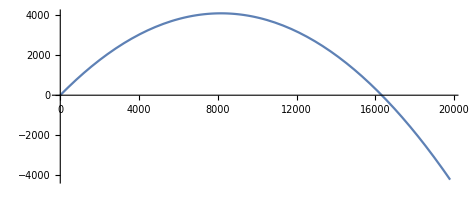

```mathematica
ParametricPlot[{t*400*Cos[π/4],t*400*Sin[π/4]-1/2 9.8 t^2},{t,0,70}]
```

b) Assuming nothing intercepts its path, at what time t will the bullet hit the ground? Find the exact time here, do not give an estimation, and express your answer in decimal form.

```mathematica
time=t/.Solve[t*400*Sin[π/4]-1/2 9.8 t^2==0][[2]]
```

```mathematica
57.723002545840615 s
```

c) How far from the gun will the bullet strike the ground? Find the exact distance here, do not give an estimation, and express your answer in decimal form.

```mathematica
time*400*Cos[π/4]
```

```mathematica
16326.530612244898m
```

### Question 2: Intersection Application

Consider two objects whose motion is defined as follows. One object is modeled by x=-(4t)/3+1, y =4+t-t^2/3, and the second object is modeled by x=4cos(t)-4,y=3sin(t)-2. Answer the following questions. 

a) Plot the two curves from t=0 to t=2π.

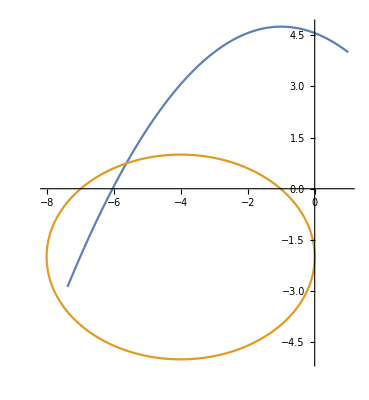

```mathematica
x1:=(-4#)/3+1&;
y1:=4+#-#^2/3&;
x2:=4Cos[#]-4&;
y2:=3Sin[#]-2&;
ParametricPlot[{{x1[t],y1[t]},{x2[t],y2[t]}},{t,0,2π}]
```

b) Find the point of intersection. Evaluate both parametric equations at the appropriate times (not necessarily the same) to show that they both go through the intersection point.

```mathematica
{time1,time2}={t1,t2}/.FindRoot[{x1[t1]==x2[t2],y1[t1]==y2[t2]},{{t1,1},{t2,-6}}]
```

{4.96766,-4.29444}

```mathematica
x1[time1]
y1[time1]
x2[time2]
y2[time2]
```

-5.62355

0.741768

-5.62355

0.741768